```mathematica
m={{0, Cos[k1],Cos[k2]},{Cos[k1],0,Cos[k1-k2]},{Cos[k2],Cos[k1-k2],0}}
```

{{0,Cos[k1],Cos[k2]},{Cos[k1],0,Cos[k1-k2]},{Cos[k2],Cos[k1-k2],0}}

```mathematica
MatrixForm[m]
```

(0 | Cos[k1] | Cos[k2]
Cos[k1] | 0 | Cos[k1-k2]
Cos[k2] | Cos[k1-k2] | 0)

```mathematica
Eigenvalues[m]
```

{-1,1/2 (1-√(3+2 Cos[2 k1]+2 Cos[2 k1-2 k2]+2 Cos[2 k2])),1/2 (1+√(3+2 Cos[2 k1]+2 Cos[2 k1-2 k2]+2 Cos[2 k2]))}

```mathematica
e[k1_,k2_,z_]:=1/2+z/2Sqrt[3+2Cos[k1]+2Cos[k1/2+Sqrt[3]/2 k2] +2Cos[k1/2+Sqrt[3]k2]]
```

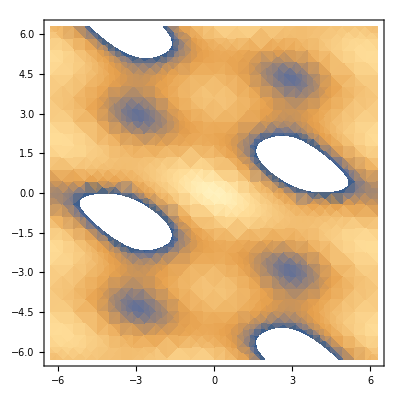

```mathematica
DensityPlot[e[k1,k2,1],{k1,-2Pi,2Pi},{k2,-2Pi,2Pi}]
```

```mathematica
Plot3D[{e[k1,k2,1],e[k1,k2,-1]},{k1,-2Pi,2Pi},{k2,-2Pi,2Pi},AxesLabel->{"k_1","k_2","E"}]
```

-Graphics3D-